```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls"
};
(*equations[pars[-8]]*)
```

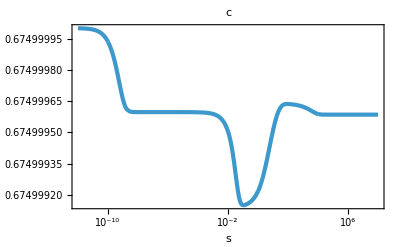
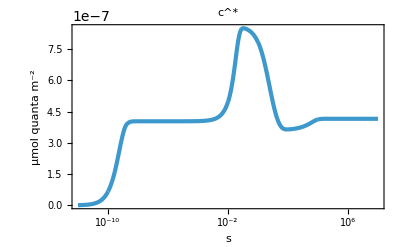
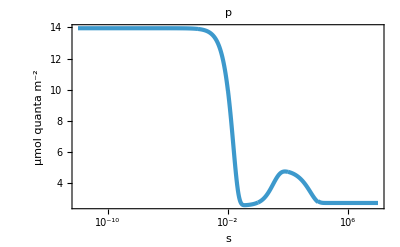
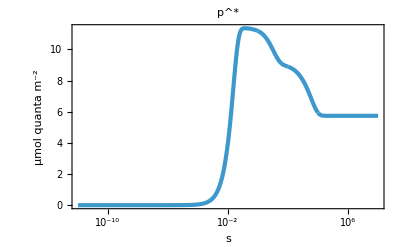
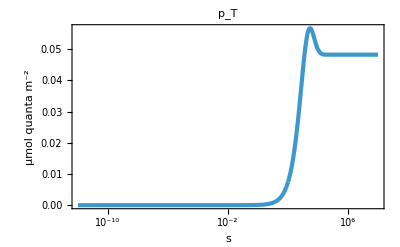
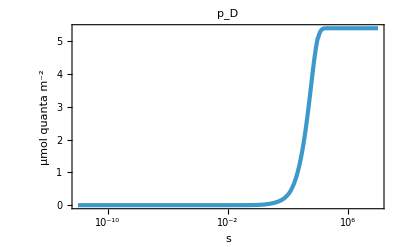
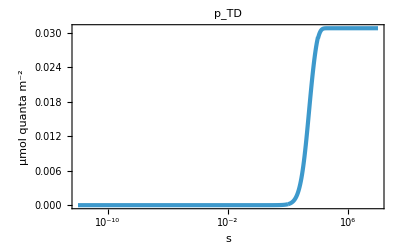
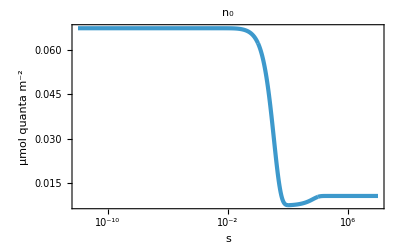

```mathematica
timeScalesParameters=Table[{Join[{L->800,tmin->0,tmax-> "tmax"/.timeRange[i]},pars[i]],{"tmin"/.timeRange[i],"tmax"/.timeRange[i]}},{i,-10,8,2}];
(Export[NotebookDirectory[]<>"Fig_7_simulation-all-time_scales/Fig_7.pdf",#];#)&@GridMap[plotSimulationStitch[#,timeScalesParameters,{imageSizePadding[ImagePaddingExtra3],FrameLabel->{{#/.units,None},{"s",None}},PlotLabel->(#/.names)}]&,quants]
```

```mathematica
γs={γC,γN,γP,γN0};
(Export[NotebookDirectory[]<>"Fig_7_simulation-all-time_scales/Fig_7_time_scaling_parameters.pdf",#];#)&@Grid[Join[{Flatten@{"t_start (s)","t_end(s)",γs/.names}},N@Table[Flatten[{timeScalePara[[2,1]],timeScalePara[[2,2]],γs/.timeScalePara[[1]]}],{timeScalePara,timeScalesParameters}]],Alignment->Left,Frame->All]
```

t_start (s) | t_end(s) | γ_C | γ_N | γ_P | γ_N_0
1.×10^-12 | 1.×10^-10 | 1. | 1. | 1. | 1.
1.×10^-10 | 1.×10^-8 | 1. | 1. | 1. | 1.
1.×10^-8 | 1.×10^-6 | 1. | 1. | 1. | 1.
1.×10^-6 | 0.0001 | 0.1 | 1. | 1. | 1.
0.0001 | 0.01 | 0.001 | 1. | 1. | 1.
0.01 | 1. | 0.00001 | 1. | 1. | 1.
1. | 100. | 1.×10^-7 | 0.1 | 1. | 1.
100. | 10000. | 1.×10^-7 | 0.001 | 0.01 | 1.
10000. | 1.×10^6 | 1.×10^-7 | 0.0001 | 0.001 | 0.1
1.×10^6 | 1.×10^8 | 1.×10^-7 | 0.0001 | 0.001 | 0.01